```mathematica
(*First we curve-fit Pfail as a function of p and L, in accordance with (A1) of Watson and Barrett (2014)*)
SetDirectory[NotebookDirectory[]];
s=Import["Data\toric_ush_crit.xlsx"][[1]];
sNames=s[[1]];
sData=s[[2;;]];

model=a+b((p-pc0)L^{1/ν0})+c((p-pc0)L^{1/ν0})^{2}+d*L^{-1/μ};
fit=NonlinearModelFit[sData,model,{a,b,{pc0,0.1028},{ν0,1.530},c,d,μ},{L,p}];
Show[ListPointPlot3D[sData,PlotStyle->Directive[Red,PointSize->.025]],Plot3D[fit[L,p],{L,5,15},{p,0.095,0.11},PlotStyle->Opacity[.75]],AxesLabel->{"L","p","Pfail"}]
fit["ParameterConfidenceIntervalTable"]
```

-Graphics3D-

| Estimate | Standard Error | Confidence Interval
a | 0.243786 | 0.00297951 | {0.237866,0.249706}
b | 1.82187 | 0.0194622 | {1.7832,1.86054}
pc0 | 0.10214 | 0.000231973 | {0.101679,0.102601}
ν0 | 1.49667 | 0.0103269 | {1.47615,1.51719}
c | 1.71033 | 0.126658 | {1.45867,1.962}
d | -0.161673 | 0.380317 | {-0.917355,0.594009}
μ | 0.401473 | 0.293038 | {-0.180788,0.983735}

```mathematica
(*Now we subtract the finite-size correction (dL^{-1/mu}) and rescale by x=(p-pc0)L^{1/nu0}*)
```

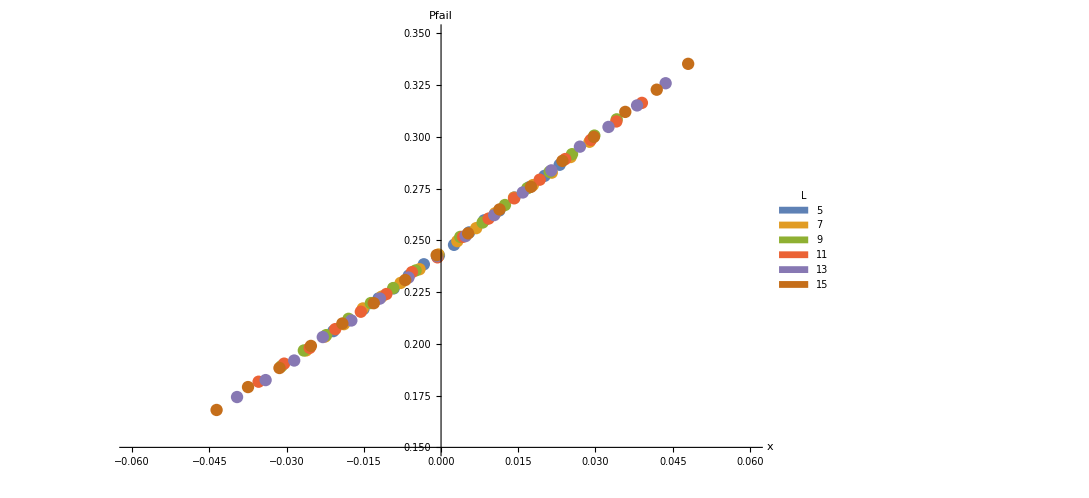

```mathematica
fitD=d/. fit["BestFitParameters"];
fitMu=μ/.fit["BestFitParameters"];
fitpc0 =pc0/. fit["BestFitParameters"];
fitNu0=ν0/. fit["BestFitParameters"];
rescaledData={sData[[;;,3]]}-fitD*{sData[[;;,1]]}^{-1/fitMu}//Flatten;
rescaledX=({sData[[;;,2]]}-fitpc0)*{sData[[;;,1]]}^{1/fitNu0}//Flatten;
DataPlot=Partition[Transpose[{rescaledX,rescaledData}],16];
DataInset=Partition[Transpose[{sData[[;;,2]],sData[[;;,3]]}],16];
plotInset=ListPlot[DataInset,Frame->True,FrameLabel->{"p","Pfail"}];
plot=ListPlot[Data,AxesLabel->{"x","Pfail"},PlotRange->{{-0.06,0.06},{0.15,0.35}},PlotLegends->Placed[SwatchLegend[Round[DeleteDuplicates[sData[[;;,1]]]],LegendLabel->"L"],Automatic],Epilog->{Inset[plotInset,{-0.03,0.3},Automatic,Scaled[.4]]}]
```

```mathematica
(*Now let's make a plot of log(Pfail)against L to show exponential dependence*)
```